```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
cr={0.45,0.55};
r=0.2;
```

```mathematica
(*test case 1*)
```

```mathematica
u01[x_,y_]:=1+(x-cr[[1]]) + 2( y-cr[[2]])
Lu01[x_,y_]:=0
gradu01[x_,y_]:={1,2}
u00[x_,y_]:=u01[x,y]^2

u1[s_]:=-2 r^2 Cos[s/r]+r^2 Sin[s/r]
```

```mathematica
(*check for u01*)
```

```mathematica
t01=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_0_1.csv"];
t01=Table[{t01[[i,2]],t01[[i,3]],t01[[i,1]]},{i,2,Length[t01]}]
```

```mathematica
δ=Max[Table[Abs[t01[[i,3]]-u01[t01[[i,1]],t01[[i,2]]]],{i,1,Length[t01]}]]
```

2.57572×10^-14

```mathematica
plotexact01=Plot3D[u01[x,y],{x,0,L},{y,0,h},PlotRange->Full,PlotStyle->{Green,Opacity[0.1]}]
```

-Graphics3D-

```mathematica
plotnum01=ListPointPlot3D[t01,PlotRange->Full,PlotStyle->{Red,PointSize->0.005}]
```

-Graphics3D-

```mathematica
Show[plotexact01,plotnum01]
```

-Graphics3D-

```mathematica
(*check for u1*)
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/u_1.csv"][[2;;]];
t1=Table[{t1[[i,2]],t1[[i,1]]},{i,2,Length[t1]}]
```

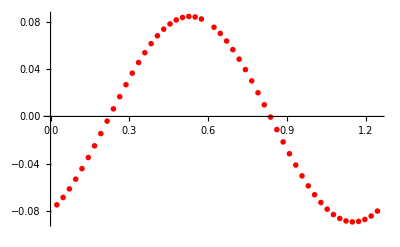

```mathematica
plotnum1=ListPlot[t1,PlotStyle->{Red,PointSize->0.01}]
```

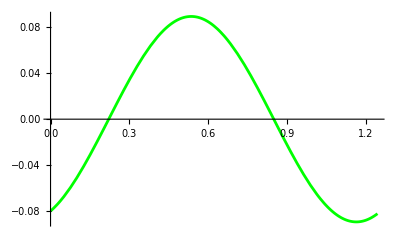

```mathematica
plotexact1=Plot[u1[x],{x,0,L1},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t1[[i,2]]-u1[t1[[i,1]]]],{i,1,Length[t1]}]]
```

0.00639301

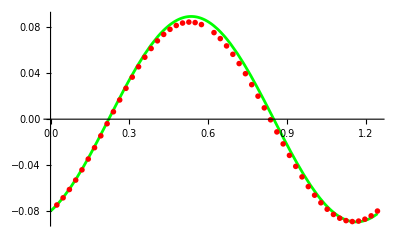

```mathematica
Show[plotexact1,plotnum1]
```